```mathematica
WriteNumber[myfile_,myx_]:=Write[myfile,If[Abs[myx]<10^-14,0.0,myx]];
WriteComplex[myfile_,myx_]:=WriteString[myfile,ToString[If[Abs[Re[myx]]<10^-14,0.0,Re[myx]],CForm]<>" "<>ToString[If[Abs[Im[myx]]<10^-14,0.0,Im[myx]],CForm]<>"\n"];
```

Unit Conversions from units I like to atomic units

```mathematica
nmperau=0.05291772108;
fsperau=0.02418884326505;
```

Physical constants in atomic units

```mathematica
eps0=0.25/π;
mu0=6.69176253 10^(-4);
cvac=137.0359991;
```

## Gaussian-Enveloped Cosine

Unitless pulse shape: u == 2 π / λ vec(k) . vec(x) - 2 π c / λ t

```mathematica
f[u_]:=Exp[-(u-m σ)^2/(2σ^2)]Cos[u];
```

Get the antiderivative... this cell MUST be evaluated before the next.

```mathematica
F[kx_,n_]=λ/(π c T)Integrate[f[u] Sin[ n π kx/(c T)-n λ u/(2c T)],{u,2π/λ kx-2π c/λ T,2π/λ kx}]
```

1/(4 c √(2 π) T)ⅈ ⅇ^(-((2 c T+n λ) σ (n λ σ+2 c T (2 ⅈ m+σ)))/(8 c^2 T^2)) λ σ (ⅇ^(σ (2 ⅈ m+(n λ σ)/(c T))) Cos[(kx n π)/(c T)] Erf[(-ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)]-ⅇ^(σ (2 ⅈ m+(n λ σ)/(c T))) Cos[(kx n π)/(c T)] Erf[(4 c^2 π T^2-ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)]-ⅇ^((ⅈ m (2 c T+n λ) σ)/(c T)) Cos[(kx n π)/(c T)] Erf[(ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)]+ⅇ^((ⅈ m (2 c T+n λ) σ)/(c T)) Cos[(kx n π)/(c T)] Erf[(4 c^2 π T^2+ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)]-ⅇ^((n λ σ (ⅈ m+σ))/(c T)) Erf[(ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m-ⅈ σ) σ))/(2 √2 c T λ σ)] (Cos[(kx n π)/(c T)]-ⅈ Sin[(kx n π)/(c T)])+ⅇ^((n λ σ (ⅈ m+σ))/(c T)) Erf[(4 c^2 π T^2+ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m-ⅈ σ) σ))/(2 √2 c T λ σ)] (Cos[(kx n π)/(c T)]-ⅈ Sin[(kx n π)/(c T)])+Erf[(-ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m-ⅈ σ) σ))/(2 √2 c T λ σ)] (Cos[(kx n π)/(c T)]+ⅈ Sin[(kx n π)/(c T)])-Erf[(4 c^2 π T^2-ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m-ⅈ σ) σ))/(2 √2 c T λ σ)] (Cos[(kx n π)/(c T)]+ⅈ Sin[(kx n π)/(c T)])+ⅈ ⅇ^(σ (2 ⅈ m+(n λ σ)/(c T))) Erf[(-ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)] Sin[(kx n π)/(c T)]-ⅈ ⅇ^(σ (2 ⅈ m+(n λ σ)/(c T))) Erf[(4 c^2 π T^2-ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)] Sin[(kx n π)/(c T)]+ⅈ ⅇ^((ⅈ m (2 c T+n λ) σ)/(c T)) Erf[(ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)] Sin[(kx n π)/(c T)]-ⅈ ⅇ^((ⅈ m (2 c T+n λ) σ)/(c T)) Erf[(4 c^2 π T^2+ⅈ n λ^2 σ^2+2 c T (-2 kx π+λ (m+ⅈ σ) σ))/(2 √2 c T λ σ)] Sin[(kx n π)/(c T)])

Simulation Constants / Box sizes

```mathematica
min=0.0;(* Minimum box position *)
max=200.0(* nm *)/nmperau; (* Maximum box position *)
λ=350.0(* nm *)/nmperau;(* Driving wavelength *)
σ=5.0;(* Unitless standard deviation *)
m=-4.0;(* Pulse spatio-temporal offset *)
T=25.0(* fs *)/fsperau;(* Fourier period *)
k={0.0,1.0,0.0};(* Wavevector *)
(* Get the maximum and minimum bounds for the 1-D function: The Table function gets the eight cube coordinates, and MapThread gets the dot product with the wavevector.  Then we apply Max, Min to get the appropriate values. *)
{dotpmin,dotpmax}={Min[#],Max[#]}&[MapThread[(k.{#1,#2,#3})&,Table[(max-min)Mod[Floor[x/2^n],2]+min,{n,0,2},{x,0,7}]]];
```

The wave-shape

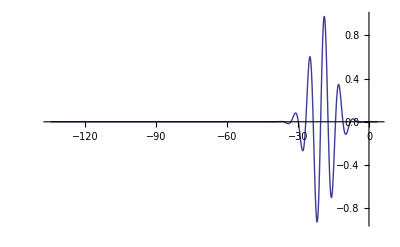

```mathematica
Plot[f[x],{x,2π/λ dotpmin-2π cvac/λ T,2Pi/λ dotpmax},PlotRange->All]
```

Which frequencies are needed?  Set thresh in the block to be the minimum norm for a component to be calculated.

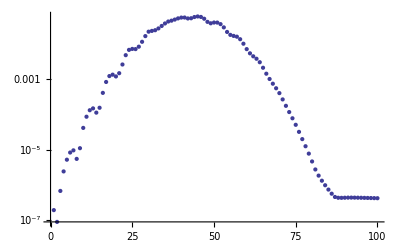

{18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67}

```mathematica
ns=Block[{thresh=10^-3,graph,list},{graph,list}=Reap[ListLogPlot[Table[{n,(If[#>thresh,Sow[n]];#)&[NIntegrate[Abs[F[x,n]/.{c->cvac}]/(dotpmax-dotpmin),{x,dotpmin,dotpmax},MaxRecursion->10]]},{n,1,100}]]];Print[Show[graph]];list[[1]]]
```

Start the file I/O: first the parameter file

```mathematica
SetDirectory["/Users/mgreuter/Builds/madness/trunk/src/apps/maxwell/data/"];
```

```mathematica
basename="EnvPulse";
```

```mathematica
file=OpenWrite[basename<>".param"];
SetOptions[file,FormatType->CForm];
```

```mathematica
WriteString[file,"Gaussian-Enveloped Cosine Pulse\n"];
WriteNumber[file,λ];
WriteNumber[file,σ];
WriteNumber[file,m];
WriteNumber[file,T];
WriteNumber[file,min];
WriteNumber[file,max];(* The simulation box size *)
WriteNumber[file,dotpmin];
WriteNumber[file,dotpmax];(* The domain for the frequency-dependent components *)
WriteNumber[file,2π/λ dotpmin-2π cvac/λ T];
WriteNumber[file,2Pi/λ dotpmax];(* The domain for the wave-shape function *)
```

Write the desired frequency indices

```mathematica
Write[file,Length[ns]];
Do[Write[file,ns[[i]]],{i,1,Length[ns]}];
```

Write the wave-shape

```mathematica
Block[{Npts=1001,h=(2Pi/λ dotpmax-(2π/λ dotpmin-2π cvac/λ T))/(Npts-1)},
Write[file,Npts];Do[WriteNumber[file,f[(2π/λ dotpmin-2π cvac/λ T)+n h]],{n,0,Npts-1}]];
```

```mathematica
Close[file];
```

Write the frequency-dependent data files

```mathematica
Do[file=OpenWrite[basename<>".freq."<>ToString[ns[[n]]]];
SetOptions[file,FormatType->CForm];

(* The frequency *)
WriteNumber[file,π ns[[n]]/T];

(* The function, preceded by the number of points *)
Block[{Npts=1001,h=(dotpmax-dotpmin)/(Npts-1)},
Write[file,Npts];
Do[WriteNumber[file,F[dotpmin+i h,ns[[n]]]/.{c->cvac}],{i,0,Npts-1}]]
Close[file],{n,1,Length[ns]}]
```

Visualize the frequency-dependent components, if desired

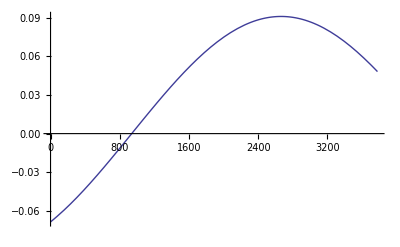

```mathematica
Plot[F[x,41]/.{c->cvac},{x,dotpmin,dotpmax},PlotRange->All]
```

```mathematica
2Pi cvac/(350/nmperau)
```

0.130181

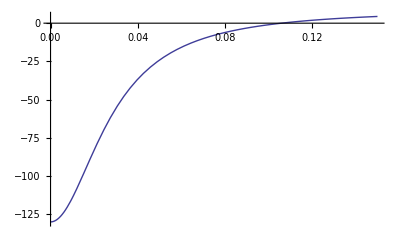

```mathematica
Plot[Re[9.07-(0.33)^2/(x^2+I 0.028x)],{x,0,0.15}]
```